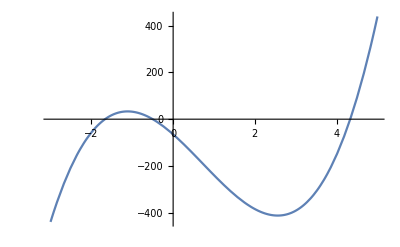

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-2, -1), (-1,0),(4, 5)

{{x→-5/3},{x→-1/2},{x→13/3}}

```mathematica
f[x_]:=18*x^3-39*x^2-154*x-65
Plot[f[x],{x,-3,5},AxesOrigin->{0,0}]
"По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах (-2, -1), (-1,0),(4, 5)"
Solve[f[x]==0]
```

```mathematica
f[x_]:=18*x^3-39*x^2-154*x-65
"Вычислим корень с помощью метода половинного деления"
a=-2;
b=-1;
e=0.001;
Do[c=(a+b)/2.;
fc=f[c];
If[f[a]*fc<0,b=c, If[fc!=0,a=c]];
If[Abs[b-a]<e||fc==0,
Print["Решение x= ", c//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}]
```

Вычислим корень с помощью метода половинного деления

Решение x= -1.66699 получено на 10 шаге.

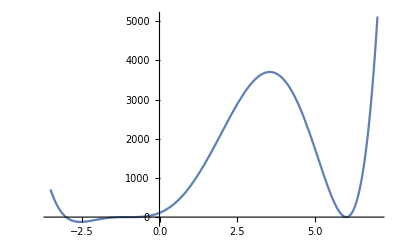

По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах ((-3.5, -2.5), (-1.5, -0.5),(5.5, 6.5)

{{x→-3},{x→-1},{x→-1},{x→-1},{x→6},{x→6}}

```mathematica
f[x_]:=x^6-6*x^5-24*x^4+82*x^3+315*x^2+324*x+108
Plot[f[x],{x,-3.5,7},AxesOrigin->{0,0}]
"По графику видно, что уравнение имеет три действительных корня. Они расположены в интервалах ((-3.5, -2.5), (-1.5, -0.5),(5.5, 6.5)"
Solve[f[x]==0]
```

```mathematica
f[x_]:=x^6-6*x^5-24*x^4+82*x^3+315*x^2+324*x+108
"Найдем один из корней с помощью метода Ньютона"
a=5.5;
b=6.5;
e=0.001;
x1=a;

Do[x2=x1;
x1=(x1-f[x1]/f'[x1])//N;
If[Abs[x2-x1]<e,
Print["Решение x= ",x2//N," получено на n = ",n," шаге."];
Break[]],
{n,1,100}]
NSolve[f[x]==0]
```

Найдем один из корней с помощью метода Ньютона

Решение x= 5.99856 получено на n = 9 шаге.

{{x→-3.},{x→-1.},{x→-1.},{x→-1.},{x→6.},{x→6.}}

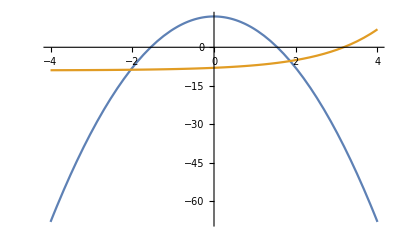

Уравнение имеет два действительных корня

Первый корень

{x→-2.03747}

Второй корень

{x→1.8634}

```mathematica
f[x_]:=12-5*x^2;
g[x_]:=2^x-9;
Plot[{f[x],g[x]},{x,-4,4},AxesOrigin->{0,0}]
"Уравнение имеет два действительных корня"
"Первый корень"
FindRoot[f[x]==g[x],{x,-2.5}]

"Второй корень"
FindRoot[f[x]==g[x],{x,1.5}]
```

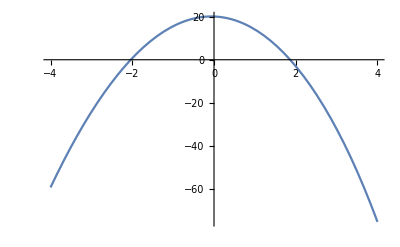

Вычислим корень с помощью метода хорд

{x→-2.03747}

{x→1.8634}

Решение x = 1.85716 получено на n = 3 шаге

```mathematica
f[x_]:=12-5*x^2-2^x+9
Plot[f[x],{x,-4,4},AxesOrigin->{0,0}]
"Вычислим корень с помощью метода хорд"
FindRoot[f[x],{x,-2.5}]
FindRoot[f[x],{x,1.5}]

a=1;
b=3;
e=0.001;
x1=a;
x2=b;


Do[
xr=x1-(f[x1]*(x2-x1)/(f[x2]-f[x1]));
If[f''[x2]*f[x2]<0,
x1=xr];
If[f''[x1]*f[x1]<0,
x2=xr];
If[Abs[x2-x1]<e,
Print["Решение x = ",xr//N," получено на n = ",n," шаге"];
Break[]],
{n,1,100}]
```